#### Calculating Spinor Coefficients C_i

Here I implement a way to calculate the spinor coefficients denoted C_i for an arbitrary number of particles with arbitrary spin

The function Coeff will attempt to calculate the desired coefficient analytically -- this works for two spin 1/2 particles and for three spin 1/2 particles
After that, the integrals are very slow to solve

NCoeff attempts to calculate C_i by numerically solving the integrals in the Coeff function. This is quite a bit faster but still gets slow after 4 or so particles

LDACoeff calculates the coefficients using the local density approximation. This is very fast even for large numbers of particles and usually has an error on the order of  10^-1 or 10^-2

```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
A[n_] = 2^((n-1)n/4)/(π^(n/4)*Sqrt[Product[Factorial[j],{j,0,n}]]);
(* W is a sequence (not a list) of the variables --- e.g., Subscript[ψ, F][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]] *)
Subscript[ψ, F][W__]:= Module[{prod,i},
prod=1;
For[i=1,i<Length[{W}],i++,prod = prod*Product[({W}[[j]]-{W}[[i]]),{j, i + 1,Length[{W}]}]];
A[Length[{W}]]*Exp[-1/2 Sum[({W}[[j]])^2,{j,1,Length[{W}]}]]*prod];
(* i denotes the desired coefficient where 1 ≤ i ≤ N - 1 and n denotes the number of particles N *)
Coeff[i_,n_] :=  Module[{X,θ,Κ,j},
X = Table[Subscript[x, j],{j,1,n}];
θ=Product[If[ j!=i , HeavisideTheta[Subscript[x, j+1]-Subscript[x, j]],1],{j,1,n-1}];
Κ=Integrate[FullSimplify[D[Subscript[ψ, F]@@X,Subscript[x, i]]^2]*DiracDelta[Subscript[x, i+1]-Subscript[x, i]]*θ,{Subscript[x, i],-Infinity, Infinity}];
For[j=1,j≤n,j++, If[j≠i,Κ=Integrate[Κ,{Subscript[x, j],-Infinity, Infinity}],1]];
Factorial[n]*Κ]
NCoeff[i_,n_] :=NCoeff[i,n]= Module[{X,θ,Κ,j,vars},
X = Table[Subscript[x, j],{j,1,n}];
θ=Product[If[ j!=i , HeavisideTheta[Subscript[x, j+1]-Subscript[x, j]],1],{j,1,n-1}];
Κ=Integrate[FullSimplify[D[Subscript[ψ, F]@@X,Subscript[x, i]]^2]*DiracDelta[Subscript[x, i+1]-Subscript[x, i]]*θ,{Subscript[x, i],-Infinity, Infinity},GenerateConditions->False];
vars=Delete[Table[Subscript[x, j],{j,1,n}],i];
Κ=NIntegrate[Κ,##]&@@({#,-∞,∞}&/@vars);
Factorial[n]*Κ]
(* This gives the local density approximation for the coefficients. Error is noticeable for N ≤ 3 but is otherwise quite good *)
LDACoeff[i_,n_]:= Block[{x,y},
x=y/.NSolve[y-2 π i/n==Sin[y]&&Im[y]==0,y][[1]];
N[1/(3π)(2*n)^(3/2)Sin[x/2]^3]]
```

#### Spin Chain Hamiltonian ℋ_sc

Here I calculate the spin chain Hamiltonian with spin dependent interaction for arbitrary number of particles (bosons or fermions) with arbitrary spin

Statevector function calculates every possible spin state in the single particle spin basis (i.e., the |s_1,m_1; s_2, m_2 ⟩  basis if it were two particles)

```mathematica
(* This function constructs our "statevector" where n is the number of particles and s is the spin, e.g., s = 1/2, 1, 3/2,... *)
StateVector[n_,s_]:= Reverse[Table[Join[Table[0,{i,1,n - Floor[Log[1+2s,If[i==0,1,i]]]-1}],IntegerDigits[i,1+2s]],{i, 0,(1+2s)^n-1}]]-s
(* Takes as input two basis elements -- i.e., a single element from matrix output of the StateVector function -- e.g., {1,0} and {0,1}. Returns 1 if state vectors are the same, 0 otherwise *)
InnerProduct[u_,v_]:=Product[Boole[u[[i]]==v[[i]]],{i,1,Length[u]}];
(* Takes bra vector u as input and performs exchange on i^th element *)
Exchange[v_,i_]:=Module[{u,t},
u=v;t = u[[i]];
u[[i]]=u[[i+1]];
u[[i+1]]=t;u]
(* This returns the exchange matrix Subscript[E, i, i+1] for a given number of particles n, an index i, and a spin s *)
𝔼[n_,i_,s_]:= Module[{𝒮},
𝒮=StateVector[n,s];
Table[InnerProduct[𝒮[[j]],Exchange[𝒮[[k]], i]],{j,1,(1+2s)^n},{k,1,(1+2s)^n}]]
(* This creates the symmetry/antisymmetry projection operator using 𝔼. Arguments represent the same things as before but now b is 1 for bosons and 0 for fermions *)
𝒫[n_,i_,s_,b_]:=IdentityMatrix[(1+2s)^n]-(-1)^b 𝔼[n,i,s];
```

Now I will create function that will project a state in the single spin basis onto the total spin basis 
ReduceStateVector[u, M] takes an output u from StateVector[n,s] and removes all basis elements that don’t have total S_z spin equal to M -- this will help simplify the Hamiltonian we need to diagonalize
TotalSpin[J, M,s ] expresses the total spin state for |J, M ⟩ in the single spin basis for two particles with spin s
TotalSpinSubProjection[J,M,s] expresses the projection operator for the Total Spin State |J,M> as a matrix --> |J,M><J,M| uing just the single particle basis states of the two particles involved
TotalSpinProjection[J,M,s,i,n] creates the projection matrix as it would be expressed using the single particle basis state for all n particles

```mathematica
ReduceStateVector[n_,s_, M_] := Part[StateVector[n,s],Flatten[Position[Table[Sum[StateVector[n,s][[k]][[ℓ]],{ℓ,1,n}]==M,{k,1,(1+2s)^n}],True]]];
TotalSpin[J_,M_,s_]:= Module[{𝒮},
𝒮=StateVector[2, s];
Table[ClebschGordan[{s,𝒮[[i]][[1]]},{s,𝒮[[i]][[2]]},{J, M}],{i, 1,Length[𝒮]}]]//Quiet
TotalSpinSubProjection[J_,M_,s_]:=Transpose[{TotalSpin[J,M,s]}].{TotalSpin[J,M,s]}
TotalSpinProjection[J_,M_,s_,i_,n_]:= Apply[TensorProduct,Delete[Table[If[i == j, TotalSpinSubProjection[J,M,s],If[j≠i+1,IdentityMatrix[(1+2s)]]],{j,1,n}],i+1]]//ArrayFlatten;
```

To start off, we will construct the spin-dependent spin-chain hamiltonian for particles with spin -1
For the three particle case, we can eliminate some variables to simplify our problem
We can eliminate C_i because they are the same for three particles
And we can rescale our Hamiltonian by g_2 and work only with G = g_2 /  g_0

```mathematica
(*Subscript[H, sc][n_, b_]:=-Sum[Subscript[C, i](1/Subscript[g, 0]*𝒫[n,i,1,b].TotalSpinProjection[0,0,1,i,n] + 
1/Subscript[g, 2]Sum[𝒫[n,i,1,b].TotalSpinProjection[2,M,1,i,n],{M,-2,2}]),{i,1,n-1}];*)
Subscript[H, sc][n_, b_]:=-Sum[(G*TotalSpinProjection[0,0,1,i,n] + 
Sum[TotalSpinProjection[2,M,1,i,n],{M,-2,2}]),{i,1,n-1}];
```

For now we are only interested in eigenstates that have S_z = 0, so we can delete rows and columns from H_sc that don’t satisfy that constraint

```mathematica
ReduceH[n_,s_,b_,m_]:=Module[{I},I=Position[Table[Sum[StateVector[n,s][[k]][[ℓ]],{ℓ,1,n}]==m,{k,1,(1+2s)^n}],False];Delete[Transpose[Delete[Transpose[Subscript[H, sc][n,b]],I]],I]]
```

```mathematica
n=3;
i=1;
s=1;
𝒫[n,i,s,1]//Dimensions
TotalSpinProjection[2,0,s,i,n]//Dimensions
Flatten[TotalSpinProjection[2,0,s,i,n],1]//MatrixForm;
Partition[Flatten[TotalSpinProjection[2,0,s,i,n],5],27]//MatrixForm;
```

{27,27}

{27,27}

```mathematica
Array[a,{2,2,2,2,2}]//Dimensions
ArrayFlatten[Array[a,{2,2,2,2,2}],2]//Dimensions
```

{2,2,2,2,2}

{4,4,2}

```mathematica
StateVector[3,1]//MatrixForm
Subscript[H, sc][3,1]//MatrixForm;
Eigensystem[Subscript[H, sc][3,1]]//Transpose//MatrixForm
```

```mathematica
n=3;
i=1;
s=1;
ReduceStateVector[n,s,0]//MatrixForm
Subscript[H, sc][n,s]//MatrixForm;
ReduceH[n,s,1,0]//Eigensystem//Transpose//MatrixForm
```

(1 | 0 | -1
1 | -1 | 0
0 | 1 | -1
0 | 0 | 0
0 | -1 | 1
-1 | 1 | 0
-1 | 0 | 1)

```mathematica
ReduceH[2,1,1,0]//Eigensystem//Transpose//MatrixForm
```

(-2 | {1,2,1}
0 | {-1,0,1}
-2 G | {1,-1,1})

```mathematica
ReduceStateVector[3,1,0]//MatrixForm
ReduceH[3,1,1,0]//Eigensystem//Transpose//MatrixForm
```

(1 | 0 | -1
1 | -1 | 0
0 | 1 | -1
0 | 0 | 0
0 | -1 | 1
-1 | 1 | 0
-1 | 0 | 1)

(-2 | {1,1,1,2,1,1,1}
-3/2 | {-1,-1/2,-1/2,0,1/2,1/2,1}
-1/2 | {0,-1,1,0,-1,1,0}
0 | {-1,1,1,0,-1,-1,1}
1/6 (-5-4 G) | {0,1,-1,0,-1,1,0}
1/12 (-7-8 G-√(49-32 G+64 G^2)) | {1,-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6+7 √(49-32 G+64 G^2)-8 G √(49-32 G+64 G^2)+1492 G^2 √(49-32 G+64 G^2)-3040 G^3 √(49-32 G+64 G^2)+2816 G^4 √(49-32 G+64 G^2)-1024 G^5 √(49-32 G+64 G^2))/(3 (7-50 G+16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6+7 √(49-32 G+64 G^2)-8 G √(49-32 G+64 G^2)+1492 G^2 √(49-32 G+64 G^2)-3040 G^3 √(49-32 G+64 G^2)+2816 G^4 √(49-32 G+64 G^2)-1024 G^5 √(49-32 G+64 G^2))/(3 (7-50 G+16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(4 (7+9 G-48 G^2+32 G^3+√(49-32 G+64 G^2)-5 G √(49-32 G+64 G^2)+4 G^2 √(49-32 G+64 G^2)))/(3 (7-50 G+16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2))),-(7+356 G-732 G^2+800 G^3-512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(7+356 G-732 G^2+800 G^3-512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),1}
1/12 (-7-8 G+√(49-32 G+64 G^2)) | {1,-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6-7 √(49-32 G+64 G^2)+8 G √(49-32 G+64 G^2)-1492 G^2 √(49-32 G+64 G^2)+3040 G^3 √(49-32 G+64 G^2)-2816 G^4 √(49-32 G+64 G^2)+1024 G^5 √(49-32 G+64 G^2))/(3 (-7+50 G-16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6-7 √(49-32 G+64 G^2)+8 G √(49-32 G+64 G^2)-1492 G^2 √(49-32 G+64 G^2)+3040 G^3 √(49-32 G+64 G^2)-2816 G^4 √(49-32 G+64 G^2)+1024 G^5 √(49-32 G+64 G^2))/(3 (-7+50 G-16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(4 (-7-9 G+48 G^2-32 G^3+√(49-32 G+64 G^2)-5 G √(49-32 G+64 G^2)+4 G^2 √(49-32 G+64 G^2)))/(3 (-7+50 G-16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2))),-(-7-356 G+732 G^2-800 G^3+512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(-7-356 G+732 G^2-800 G^3+512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),1})

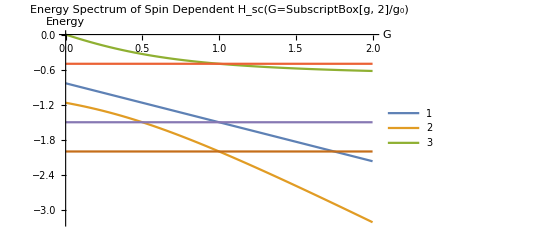

```mathematica
Plot[{1/6 (-5-4 G),1/12 (-7-8 G-√(49-32 G+64 G^2)),1/12 (-7-8 G+√(49-32 G+64 G^2)),-1/2,-3/2,-2},{G,0,2},PlotLegends->{"1","2","3"},PlotLabel->"Energy Spectrum of Spin Dependent H_sc(G=SubscriptBox[g, 2]/g_0)",AxesLabel->{"G", "Energy"}]
```

```mathematica
ReduceStateVector[3,1,0]//MatrixForm
ReduceH[3,1,1,0]//Eigensystem//Transpose//MatrixForm
```

(1 | 0 | -1
1 | -1 | 0
0 | 1 | -1
0 | 0 | 0
0 | -1 | 1
-1 | 1 | 0
-1 | 0 | 1)

(-4 | {1,1,1,2,1,1,1}
-3 | {-1,-1/2,-1/2,0,1/2,1/2,1}
-1 | {0,-1,1,0,-1,1,0}
0 | {-1,1,1,0,-1,-1,1}
1/3 (-5-4 G) | {0,1,-1,0,-1,1,0}
1/6 (-7-8 G-√(49-32 G+64 G^2)) | {1,-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6+7 √(49-32 G+64 G^2)-8 G √(49-32 G+64 G^2)+1492 G^2 √(49-32 G+64 G^2)-3040 G^3 √(49-32 G+64 G^2)+2816 G^4 √(49-32 G+64 G^2)-1024 G^5 √(49-32 G+64 G^2))/(3 (7-50 G+16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6+7 √(49-32 G+64 G^2)-8 G √(49-32 G+64 G^2)+1492 G^2 √(49-32 G+64 G^2)-3040 G^3 √(49-32 G+64 G^2)+2816 G^4 √(49-32 G+64 G^2)-1024 G^5 √(49-32 G+64 G^2))/(3 (7-50 G+16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(4 (7+9 G-48 G^2+32 G^3+√(49-32 G+64 G^2)-5 G √(49-32 G+64 G^2)+4 G^2 √(49-32 G+64 G^2)))/(3 (7-50 G+16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2))),-(7+356 G-732 G^2+800 G^3-512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(7+356 G-732 G^2+800 G^3-512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),1}
1/6 (-7-8 G+√(49-32 G+64 G^2)) | {1,-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6-7 √(49-32 G+64 G^2)+8 G √(49-32 G+64 G^2)-1492 G^2 √(49-32 G+64 G^2)+3040 G^3 √(49-32 G+64 G^2)-2816 G^4 √(49-32 G+64 G^2)+1024 G^5 √(49-32 G+64 G^2))/(3 (-7+50 G-16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6-7 √(49-32 G+64 G^2)+8 G √(49-32 G+64 G^2)-1492 G^2 √(49-32 G+64 G^2)+3040 G^3 √(49-32 G+64 G^2)-2816 G^4 √(49-32 G+64 G^2)+1024 G^5 √(49-32 G+64 G^2))/(3 (-7+50 G-16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(4 (-7-9 G+48 G^2-32 G^3+√(49-32 G+64 G^2)-5 G √(49-32 G+64 G^2)+4 G^2 √(49-32 G+64 G^2)))/(3 (-7+50 G-16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2))),-(-7-356 G+732 G^2-800 G^3+512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(-7-356 G+732 G^2-800 G^3+512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),1})

```mathematica
D[Tanh[x],{x,2}]
```

-2 Sech[x]^2 Tanh[x]

```mathematica
f[x_,t_] = C*Tanh[Sqrt[g]*x]
FullSimplify[-1/2*D[f[x,t],{x,2}]+g*Abs[f[x,t]]^2*f[x,t],Assumptions->{Im[C]==0,Im[g]==0,Im[t]==0}]
```

C Tanh[√g x]

C g (Abs[C Tanh[√g x]]^2+Sech[√g x]^2) Tanh[√g x]